Coset Characters
Here we calculate the characters of the Coset CFT using a bunch of truncated string functions.
I used this: https://arxiv.org/pdf/hep-th/9201078#:~:text=n,η%28τ%29%5D to calculate the characters.

```mathematica
k=8;
c=(2(k-1))/(k+2);
h[l_,m_]:=(l(l+2))/(4(k+2))-m^2/(4k);
ηinv[q_,N_:∞]:=q^(-1/24)∑_(k=0)^N PartitionsP[k] q^k;
χ[l_,m_,q_,N_:∞]:=ηinv[q,N]^2 q^(h[l,m]+1/(4(k+2)))∑_(r=0)^N ∑_(s=0)^N (-1)^(r+s)q^(r(r+1)/2+s(s+1)/2+r s(k+1))(q^(r(l+m)/2+s(l-m)/2)-q^(k+1-l + r(k+1-l/2-m/2)+s(k+1-l/2+m/2)));
χsq[l_,m_,q_,N_:∞]:=Abs[χ[l,m,q,N]]^2;
Z[q_,W_,N_:∞]:=Total[Map[Function[w,χsq[w[[1]],w[[2]],q,N]],W]];
```

Coset Model Partition Function
The partition function of the coset CFT. This is the A_(k+1)modular invariant. We will calculate the other one later.

```mathematica
w=ConstantArray[0,{k+1,2k+1}];
M[m_]:=m+k+1;
L[l_]:=l+1
For[l=0,l<=k,l++,For[m=-l,m<=l,m=m+2,If[w[[L[l],M[m]]]==0,
w[[L[l],M[m]]]=1;
If[0<M[k-m]<=2k+1,w[[L[k-l],M[k-m]]]=-1];If[0<M[k+m]<=2k+1,w[[L[k-l],M[k+m]]]=-1];
]]]
W={#[[1]]-1,#[[2]]-k-1}&/@Position[w,_?(# ==1&),{2}];
n=10;
Assuming[q>0,Series[Z[q,W,n],{q,0,1}]]
```

1/q^(7/60)+2/q^(7/240)+2 q^(1/30)+2 q^(17/240)+q^(1/12)+q^(17/60)+2 q^(137/240)+2 q^(5/6)+4 q^(233/240)+O[q]^(241/240)

Nondiagonal Modular Invariant
There is another modular invariant we can find in this theory. It is D_k modular invariant that is given as follows.

The Modular S matrix of the Coset Model
In our effort to find the Cardy states in the gauged theory we want to calculate the S matrix and express the Cardy states as linear combinations of the Ishibashi states in the coset model using coefficients from the S-matrix. The matrix is given by

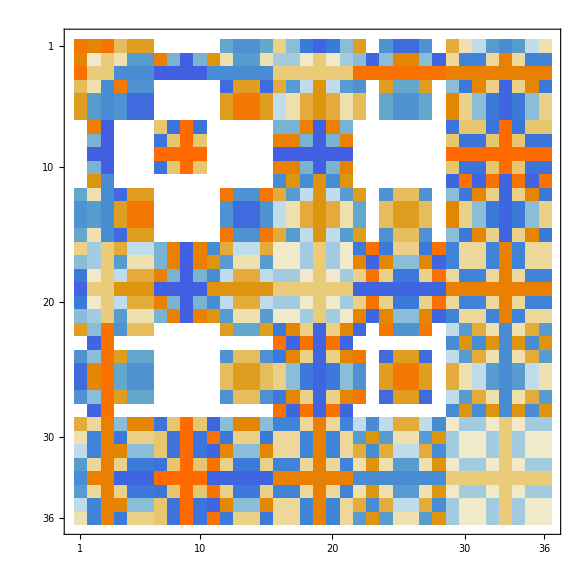

```mathematica
S=Array[(1/(√(2(k+2)))Sin[(π(W[[#1,1]]+1)(W[[#2,1]]+1))/(k+2)] ⅇ^(-ⅈ π (W[[#1,2]]W[[#2,2]])/(k+2)))&,{Length[W],Length[W]}]//Simplify;
S//MatrixPlot
```